```mathematica
f2=1-f1
```

1-f1

```mathematica
m=n f1 d1(1-c1)+n f2 d2(1-c2)
```

(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n

```mathematica
h1=Simplify[n(1-d1)/(n(1-d1)+m)]
```

(-1+d1)/(-1+d1 (1+(-1+c1) f1)+d2 (-1+c2+f1-c2 f1))

```mathematica
h2=Simplify[n(1-d2)/(n(1-d2)+m)]
```

(-1+d2)/(-1+(-1+c1) d1 f1+d2 f1+c2 (d2-d2 f1))

```mathematica
rans=Simplify[Solve[r==((f1(h1^2)+f2(h2^2))/(f1+f2))((1/n)+((n-1)/n)r),r][[1]]]
```

{r→(((-1+d1)^2 f1)/(-1+d1 (1+(-1+c1) f1)+d2 (-1+c2+f1-c2 f1))^2+((-1+d2)^2 (1-f1))/(-1+(-1+c1) d1 f1+d2 f1+c2 (d2-d2 f1))^2)/((1-((((-1+d1)^2 f1)/(-1+d1 (1+(-1+c1) f1)+d2 (-1+c2+f1-c2 f1))^2+((-1+d2)^2 (1-f1))/(-1+(-1+c1) d1 f1+d2 f1+c2 (d2-d2 f1))^2) (-1+n))/n) n)}

```mathematica
w1=n(1-d1i)/(n(1-d1loc)+m)+n d1i(1-c1)(f1 (1/(n(1-d1)+m))+f2(1/(n(1-d2)+m)))
```

((1-d1i) n)/((1-d1loc) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)+(1-c1) d1i n (f1/((1-d1) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)+(1-f1)/((1-d2) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n))

```mathematica
w2=n(1-d2i)/(n(1-d2loc)+m)+n d2i(1-c2)(f1 (1/(n(1-d1)+m))+f2(1/(n(1-d2)+m)))
```

((1-d2i) n)/((1-d2loc) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)+(1-c2) d2i n (f1/((1-d1) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)+(1-f1)/((1-d2) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n))

```mathematica
w=f1 w1+f2 w2
```

f1 (((1-d1i) n)/((1-d1loc) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)+(1-c1) d1i n (f1/((1-d1) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)+(1-f1)/((1-d2) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)))+(1-f1) (((1-d2i) n)/((1-d2loc) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)+(1-c2) d2i n (f1/((1-d1) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)+(1-f1)/((1-d2) n+(1-c2) d2 (1-f1) n+(1-c1) d1 f1 n)))

```mathematica
dw1mat[n_,c1_,c2_,d1_,d2_]=Simplify[((1+((1/n)+((n-1)/n)r))/2)D[w,d1i]+((1/n)+((n-1)/n)r)D[w,d1loc]/.{d1i->d1,d1loc->d1,d2i->d2,d2loc->d2}/.rans/.f1->1/2];
```

```mathematica
dw2mat[n_,c1_,c2_,d1_,d2_]=Simplify[((1+((1/n)+((n-1)/n)r))/2)D[w,d2i]+((1/n)+((n-1)/n)r)D[w,d2loc]/.{d1i->d1,d1loc->d1,d2i->d2,d2loc->d2}/.rans/.f1->1/2];
```

```mathematica
dw1off[n_,c1_,c2_,d1_,d2_]=Simplify[D[w,d1i]+((1/n)+((n-1)/n)r)D[w,d1loc]/.{d1i->d1,d1loc->d1,d2i->d2,d2loc->d2}/.rans/.f1->1/2];
```

```mathematica
dw2off[n_,c1_,c2_,d1_,d2_]=Simplify[D[w,d2i]+((1/n)+((n-1)/n)r)D[w,d2loc]/.{d1i->d1,d1loc->d1,d2i->d2,d2loc->d2}/.rans/.f1->1/2];
```

```mathematica
solmat[n_,c1_,c2_]:=(Clear[a1];
a1={d1,d2}/.FindRoot[{dw1mat[n,c1,c2,d1,d2]==0,dw2mat[n,c1,c2,d1,d2]==0},{d1,0.5},{d2,0.3}];
If[a1[[1]]>0,If[a1[[2]]>0,a1,{d1,0}/.FindRoot[dw1mat[n,c1,c2,d1,0]==0,{d1,0.5}]],{0,d2}/.FindRoot[dw2mat[n,c1,c2,0,d2]==0,{d2,0.5}]]
)
```

```mathematica
soloff[n_,c1_,c2_]:=(Clear[a1];
a1={d1,d2}/.FindRoot[{dw1off[n,c1,c2,d1,d2]==0,dw2off[n,c1,c2,d1,d2]==0},{d1,0.5},{d2,0.3}];
If[a1[[1]]>0,If[a1[[2]]>0,a1,{d1,0}/.FindRoot[dw1off[n,c1,c2,d1,0]==0,{d1,0.5}]],{0,d2}/.FindRoot[dw2off[n,c1,c2,0,d2]==0,{d2,0.5}]]
)
```

```mathematica
solmat[5,0.1,0.1]
solmat[5,0.1,0.2]
```

{0.737041,0.737041}

{0.676032,0.591493}

```mathematica
soloff[5,0.1,0.1]
soloff[5,0.1,0.2]
```

{0.598508,0.598508}

{0.524182,0.427906}

```mathematica
fig1=Plot3D[solmat[5,c1,c2][[1]],{c1,0,1},{c2,0,1},PlotRange->{0.00001,1},PlotPoints->50,PlotStyle->{Blue,Opacity[0.5]}]
```

-Graphics3D-

```mathematica
fig1f=Show[fig1,AxesLabel->{"c_1","  c_2","d_1  "},PlotLabel->"MATERNAL CONTROL
"]
```

-Graphics3D-

```mathematica
fig2=Plot3D[soloff[5,c1,c2][[1]],{c1,0,1},{c2,0,1},PlotRange->{0.00001,1},PlotPoints->50,PlotStyle->{Red,Opacity[0.5]}]
```

-Graphics3D-

```mathematica
fig2f=Show[fig2,AxesLabel->{"c_1","  c_2","d_1  "},PlotLabel->"OFFSPRING CONTROL
"]
```

-Graphics3D-

```mathematica
fig3f=Show[fig1,fig2,AxesLabel->{"c_1","c_2","d_1"},PlotLabel->"MATERNAL VS OFFSPRING CONTROL
"]
```

-Graphics3D-

```mathematica
Show[GraphicsArray[{fig1f,fig2f}]]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

-Graphics-

```mathematica
solmat[5,0,0.4]
soloff[5,0,0.4]
```

{0.691157,0.312656}

{0.554824,0.120975}

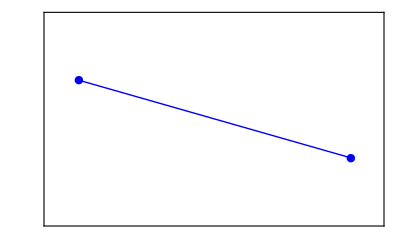

```mathematica
fig1a=ListPlot[solmat[5,0,0.4],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,FrameTicks->None,Joined->True,PlotStyle->{Blue},BaseStyle->{FontSize->16}]
```

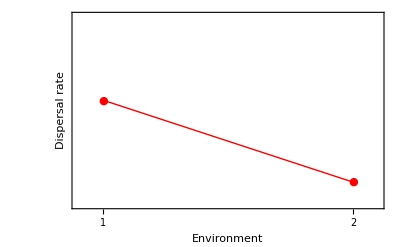

```mathematica
fig1b=ListPlot[soloff[5,0,0.4],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,Joined->True,PlotStyle->{Red},FrameLabel->{"Environment","Dispersal rate"},FrameTicks->{{1,2},None,None,None},BaseStyle->{FontSize->16}]
```

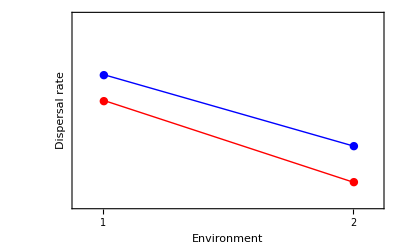

```mathematica
fig1=Show[fig1b,fig1a]
```

```mathematica
dwsig[n_,c1_,c2_,{s1_,s2_,ds_,dns_}]:={(ds-dns)dw1mat[n,c1,c2,s1 ds+(1-s1)dns,s2 ds+(1-s2)dns],(ds-dns)dw2mat[n,c1,c2,s1 ds+(1-s1)dns,s2 ds+(1-s2)dns],s1 dw1off[n,c1,c2,s1 ds+(1-s1)dns,s2 ds+(1-s2)dns]+s2 dw2off[n,c1,c2,s1 ds+(1-s1)dns,s2 ds+(1-s2)dns],(1-s1)dw1off[n,c1,c2,s1 ds+(1-s1)dns,s2 ds+(1-s2)dns]+(1-s2) dw2off[n,c1,c2,s1 ds+(1-s1)dns,s2 ds+(1-s2)dns]}
```

```mathematica
evol[n_,c1_,c2_,init_,t_,tt_]:=(Clear[upd];
upd[strat_]:=Clip[strat+dwsig[n,c1,c2,strat],{0.0001,0.9999}];
nupd[strat_]:=Nest[upd,strat,tt];
sol=Nest[nupd,init,Floor[t/tt]];
{{sol[[1]]sol[[3]]+(1-sol[[1]])sol[[4]],sol[[2]]sol[[3]]+(1-sol[[2]])sol[[4]]},sol}
)
```

```mathematica
evolfp[n_,c1_,c2_,init_]:=(Clear[upd,std];
upd[strat_]:=Clip[strat+dwsig[n,c1,c2,strat],{0.0001,0.9999}];
sol=FixedPoint[upd,init,SameTest->(Max[Map[Abs,#1-#2]]<10^-5&)];
{{sol[[1]]sol[[3]]+(1-sol[[1]])sol[[4]],sol[[2]]sol[[3]]+(1-sol[[2]])sol[[4]]},sol}
)
```

```mathematica
ent[p_]=If[p==0,0,If[p==1,0,-(p Log[2,p]+(1-p)Log[2,1-p])]]
```

If[p==0,0,If[p==1,0,-(p Log[2,p]+(1-p) Log[2,1-p])]]

```mathematica
siginfo[p1_,p2_]=1-(((p1+p2)/2)ent[p1/(p1+p2)]+(1-((p1+p2)/2))ent[(1-p1)/((1-p1)+(1-p2))])
```

1-(1+1/2 (-p1-p2)) If[(1-p1)/(2-p1-p2)==0,0,If[(1-p1)/(2-p1-p2)==1,0,-(((1-p1) Log[2,(1-p1)/(2-p1-p2)])/(2-p1-p2)+(1-(1-p1)/(2-p1-p2)) Log[2,1-(1-p1)/(2-p1-p2)])]]-1/2 (p1+p2) If[p1/(p1+p2)==0,0,If[p1/(p1+p2)==1,0,-((p1 Log[2,p1/(p1+p2)])/(p1+p2)+(1-p1/(p1+p2)) Log[2,1-p1/(p1+p2)])]]

```mathematica
ansfull=Table[{c1,c2,evolfp[5,c1,c2,If[c1<c2,{0.9,0.1,0.9,0.1},{0.1,0.9,0.9,0.1}]]},{c2,0.001,1,0.02},{c1,0.001,1,0.02}];
```

```mathematica
ans1=Table[{c1,c2,evolfp[5,c1,c2,If[c1<c2,{0.9,0.1,0.9,0.1},{0.1,0.9,0.9,0.1}]][[1,1]]},{c2,0.001,1,0.02},{c1,0.001,1,0.02}];
```

```mathematica
anstemp=Flatten[ansfull,1];
```

```mathematica
ansinfo=Table[{anstemp[[i,1]],anstemp[[i,2]],siginfo[anstemp[[i,3,2,1]],anstemp[[i,3,2,2]]]},{i,2500}];
```

```mathematica
tidy=Table[{anstemp[[i,1]],anstemp[[i,2]],If[anstemp[[i,1]]==anstemp[[i,2]],0,siginfo[anstemp[[i,3,2,1]],anstemp[[i,3,2,2]]]]},{i,2500}];
```

```mathematica
f2a=ListPlot3D[Flatten [ans1,1]]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[f2a,AxesLabel->{"c_1","  c_2","d_1  "},PlotLabel->"DISPERSAL WHEN OFFSPRING RELY ON MATERNAL SIGNALS
"]
```

-Graphics3D-

```mathematica
f2b=ListPlot3D[ansinfo]
```

-Graphics3D-

```mathematica
f2b=ListPlot3D[tidy]
```

-Graphics3D-

```mathematica
f2b=ListContourPlot[tidy,Contours->{0.001,0.99},InterpolationOrder->5]
```

-Graphics-

```mathematica
evol[5,0.02,0.04,{0.9,0.1,0.9,0.1},300,10]
evol[5,0.02,0.04,{0.9,0.1,0.9,0.1},500,10]
evol[5,0.02,0.04,{0.9,0.1,0.9,0.1},1000,10]
evol[5,0.02,0.04,{0.9,0.1,0.9,0.1},5000,10]
evol[5,0.02,0.04,{0.9,0.1,0.9,0.1},10000,10]
```

{{0.864858,0.847863},{0.923175,0.511155,0.868027,0.826778}}

{{0.864856,0.847871},{0.971856,0.563923,0.866028,0.824391}}

{{0.864769,0.848335},{0.9999,0.711392,0.864774,0.807815}}

{{0.856394,0.856394},{0.9999,0.9999,0.856407,0.726882}}

{{0.856394,0.856394},{0.9999,0.9999,0.856407,0.726882}}

```mathematica
Max[Map[Abs,(evol[5,0.02,0.04,{0.9,0.1,0.9,0.1},500,1][[2]]-evol[5,0.02,0.04,{0.9,0.1,0.9,0.1},501,1][[2]])]]
```

0.000265027

```mathematica
Max[Map[Abs,(evol[5,0.02,0.04,{0.9,0.1,0.9,0.1},1500,1][[2]]-evol[5,0.02,0.04,{0.9,0.1,0.9,0.1},1501,1][[2]])]]
```

0.000519677

```mathematica
solmat[5,0,0.4]
```

{0.691157,0.312656}

```mathematica
soloff[5,0,0.4]
```

{0.554824,0.120975}

```mathematica
evol[5,0,0.4,{0.9,0.1,0.9,0.1},300,10]
```

{{0.539619,0.274973},{0.9999,0.509427,0.539673,0.0001}}

```mathematica
solmat[5,0.6,0.1]
soloff[5,0.6,0.1]
evol[5,0.6,0.1,{0.1,0.9,0.9,0.1},300,10]
evol[5,0.1,0.6,{0.9,0.1,0.9,0.1},300,10]
```

{0,0.582754}

{0,0.468658}

{{0.00014686,0.468652},{0.0001,0.9999,0.468699,0.0001}}

{{0.468652,0.00014686},{0.9999,0.0001,0.468699,0.0001}}

```mathematica
solmat[5,0.6,0.2]
soloff[5,0.6,0.2]
evol[5,0.6,0.2,{0.1,0.9,0.9,0.1},300,10]
```

{0.00439651,0.528644}

{0,0.409469}

{{0.0493467,0.394842},{0.124744,0.9999,0.394881,0.0001}}

```mathematica
evol[5,0.125,0.25,{0.9,0.1,0.9,0.1},350,10][[2]]
```

{0.9999,0.9999,0.414324,0.0500079}

```mathematica
evol[5,0.1,0.8,{0.9,0.1,0.9,0.1},300,10]
```

{{0.468647,0.000146859},{0.9999,0.0001,0.468694,0.0001}}

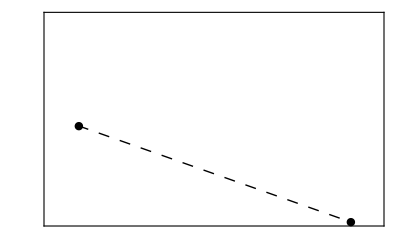

```mathematica
fig2a=ListPlot[evol[5,0.1,0.8,{0.9,0.1,0.9,0.1},300,10][[1]],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,FrameTicks->None,Joined->True,PlotStyle->{Black,Dashing[{0.02,0.02}]},BaseStyle->{FontSize->16}]
```

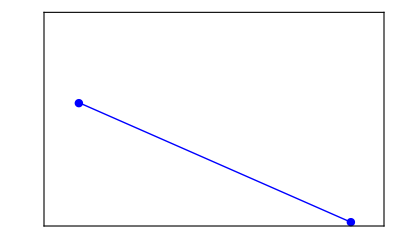

```mathematica
fig2b=ListPlot[solmat[5,0.1,0.8],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,FrameTicks->None,Joined->True,PlotStyle->{Blue}]
```

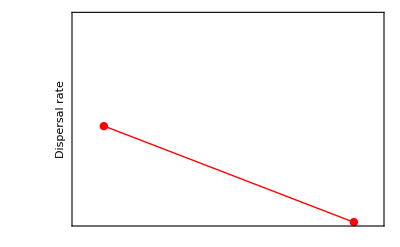

```mathematica
fig2c=ListPlot[soloff[5,0.1,0.8],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,Joined->True,PlotStyle->{Red},FrameLabel->{"","Dispersal rate"},FrameTicks->{None,None,None,None},BaseStyle->{FontSize->16}]
```

```mathematica
Take[{a,b,c},2]
```

{a,b}

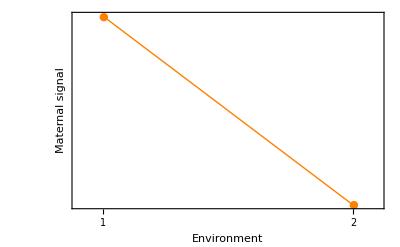

```mathematica
fig22a=ListPlot[Take[evol[5,0.1,0.8,{0.9,0.1,0.9,0.1},300,10][[2]],2],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Joined->True,PlotStyle->{Orange},BaseStyle->{FontSize->16},Frame->True,FrameTicks->{{1,2},None,None,None},BaseStyle->{FontSize->16},FrameLabel->{"Environment","Maternal signal"}]
```

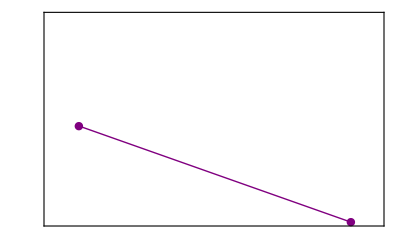

```mathematica
fig22b=ListPlot[Take[evol[5,0.1,0.8,{0.9,0.1,0.9,0.1},300,10][[2]],-2],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,FrameTicks->None,Joined->True,PlotStyle->{Purple},BaseStyle->{FontSize->16}]
```

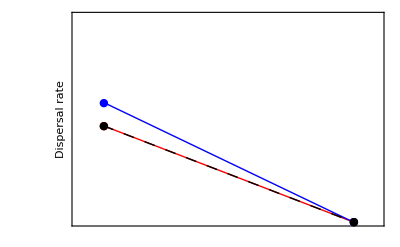

```mathematica
fig2=Show[{fig2c,fig2b,fig2a}]
```

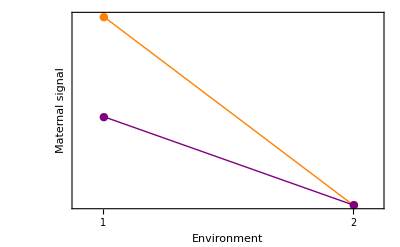

```mathematica
fig22=Show[{fig22a,fig22b}]
```

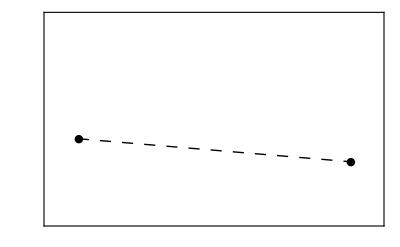

```mathematica
fig3a=ListPlot[evol[5,0.1,0.4,{0.9,0.1,0.9,0.1},300,10][[1]],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,FrameTicks->None,Joined->True,PlotStyle->{Black,Dashing[{0.02,0.02}]},BaseStyle->{FontSize->16}]
```

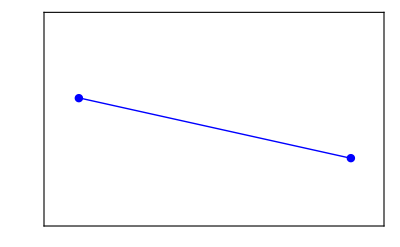

```mathematica
fig3b=ListPlot[solmat[5,0.1,0.4],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,FrameTicks->None,Joined->True,PlotStyle->{Blue}]
```

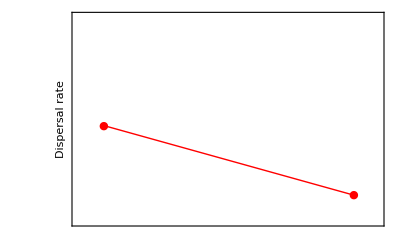

```mathematica
fig3c=ListPlot[soloff[5,0.1,0.4],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,Joined->True,PlotStyle->{Red},FrameLabel->{"","Dispersal rate"},FrameTicks->{None,None,None,None},BaseStyle->{FontSize->16}]
```

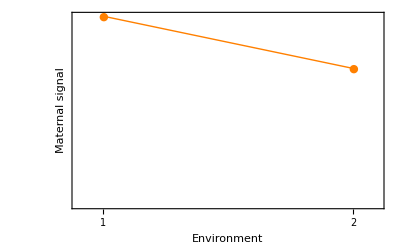

```mathematica
fig32a=ListPlot[Take[evol[5,0.1,0.4,{0.9,0.1,0.9,0.1},300,10][[2]],2],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,Joined->True,PlotStyle->{Orange},BaseStyle->{FontSize->16},FrameLabel->{"Environment","Maternal signal"},FrameTicks->{{1,2},None,None,None},BaseStyle->{FontSize->16}]
```

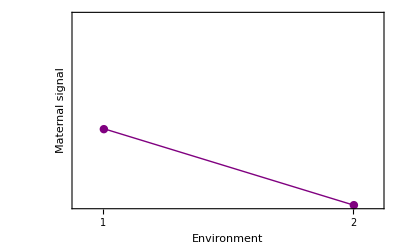

```mathematica
fig32b=ListPlot[Take[evol[5,0.1,0.4,{0.9,0.1,0.9,0.1},300,10][[2]],-2],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,Joined->True,PlotStyle->{Purple},FrameLabel->{"Environment","Maternal signal"},FrameTicks->{{1,2},None,None,None},BaseStyle->{FontSize->16}]
```

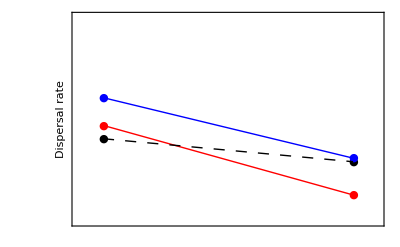

```mathematica
fig3=Show[{fig3c,fig3b,fig3a}]
```

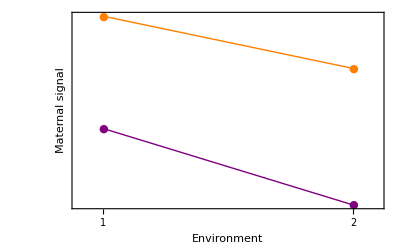

```mathematica
fig32=Show[{fig32a,fig32b}]
```

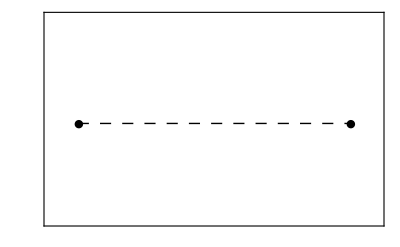

```mathematica
fig4a=ListPlot[evol[5,0.1,0.2,{0.9,0.1,0.9,0.1},300,10][[1]],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,FrameTicks->None,Joined->True,PlotStyle->{Black,Dashing[{0.02,0.02}]}]
```

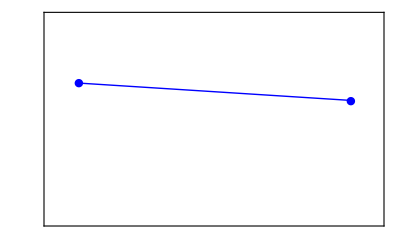

```mathematica
fig4b=ListPlot[solmat[5,0.1,0.2],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,FrameTicks->None,Joined->True,PlotStyle->{Blue}]
```

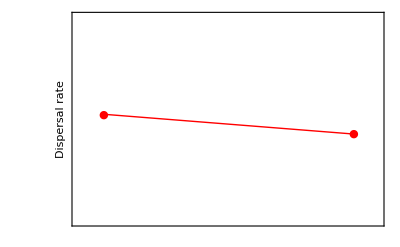

```mathematica
fig4c=ListPlot[soloff[5,0.1,0.2],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1}},Frame->True,Joined->True,PlotStyle->{Red},FrameLabel->{"","Dispersal rate"},FrameTicks->{None,None,None,None},BaseStyle->{FontSize->16}]
```

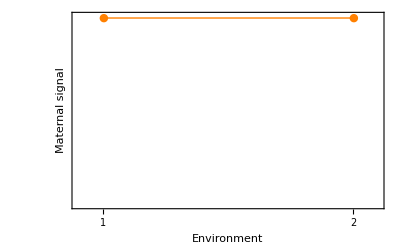

```mathematica
fig42a=ListPlot[Take[evol[5,0.1,0.2,{0.9,0.1,0.9,0.1},300,10][[2]],2],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1.01}},Frame->True,Joined->True,PlotStyle->{Orange},BaseStyle->{FontSize->16},FrameLabel->{"Environment","Maternal signal"},FrameTicks->{{1,2},None,None,None},BaseStyle->{FontSize->16}]
```

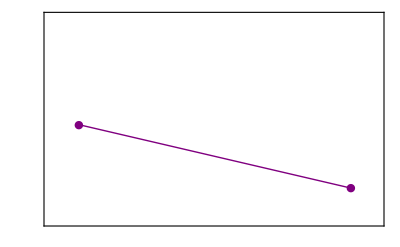

```mathematica
fig42b=ListPlot[Take[evol[5,0.1,0.2,{0.9,0.1,0.9,0.1},300,10][[2]],-2],PlotMarkers->{Automatic,Large},PlotRange->{{0.9,2.1},{0,1.01}},Frame->True,Joined->True,PlotStyle->{Purple},BaseStyle->{FontSize->16},FrameTicks->None]
```

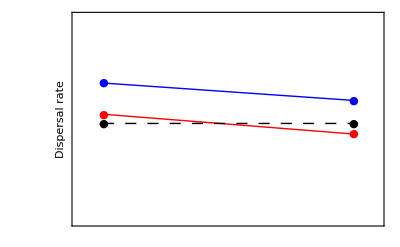

```mathematica
fig4=Show[{fig4c,fig4b,fig4a}]
```

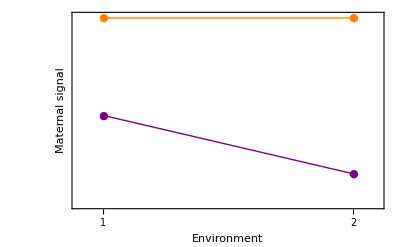

```mathematica
fig42=Show[{fig42a,fig42b}]
```

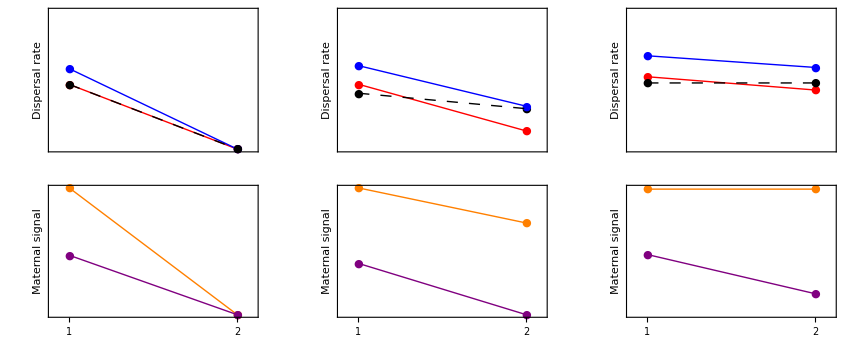

```mathematica
Show[GraphicsGrid[{{fig2,fig3,fig4},{fig22,fig32,fig42}}]]
```